```mathematica
(* Graphical Method. *)
(* Que: Minimize 2x+y
s.t. 5x+10y≤50
	 x+y≥1
	  y≤4
	  x≥0
	  y≥0
*)

Minimize[{ 2x+y,5x+10y≤50 && x+y≥1 && y≤4 && x≥0 && y≥0 },{x,y}]
```

{1,{x→0,y→1}}

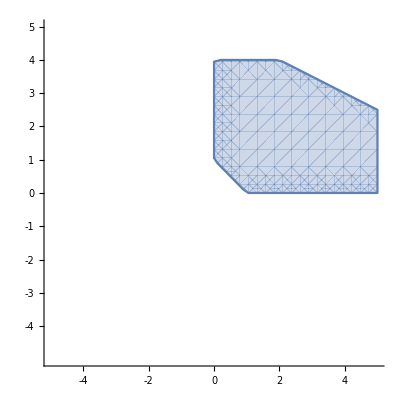

```mathematica
RegionPlot[{ 5x+10 y≤50 && x+y≥1 && y≤4 && x≥0 && y≥0 },{x,-5,5},{y,-5,5},Frame->False,Axes->True,Ticks->{{-4,-3,-2,-1,0,1,2,3,4},{-4,-3,-2,-1,0,1,2,3,4,5}}]
```